{8/4687,25/4687,68/4687,236/4687,510/4687,955/4687,1177/4687,1708/4687}

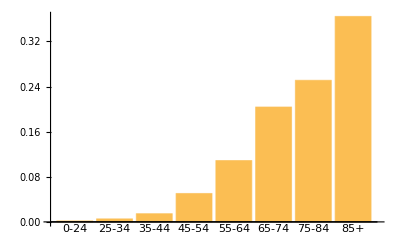

hospitalization[all]→9/10000

hospitalization[65+]→273/100000

{tests[total]→12600000,tests[positive]→1379000}

```mathematica
$data={{"0-24",8},
{"25-34",25},
{"35-44",68},
{"45-54",236},
{"55-64",510},
{"65-74",955},
{"75-84",1177},
{"85+",1708}
};
$label=First/@$data;
$values=Last/@$data;
$total=Apply[Plus,$values];
$values=$values/$total
BarChart[$values,ChartLabels->$label]
hospitalization["all"]->90/100000
hospitalization["65+"]->273/100000
$s={tests["total"]->12600000,
tests["positive"]->1379000}
```